# Lorenz System

## Lorenz Experiment: σ=10, β=8/3, ρ=28, x(0)=0, y(0)=1, z(0)=0.

```mathematica
Import["/Users/miguelangel/atractor3D.txt","Table"]
```

{{0.,1.,0.},{0.0951214,1.00354,0.000479006},{0.182772,1.03242,0.00186843},6996,{-3.96195,-6.09038,18.6546},{-4.1799,-6.41328,18.4149}}
 |  |  |  |

```mathematica
a=Graphics3D[{ColorData[1][1],Thickness[Medium],Line[%1]},Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
Import["/Users/miguelangel/atractor2D.txt","Table"]
```

{{0.,0.},{0.0951214,0.000479006},{0.182772,0.00186843},{0.265977,0.00416733},6994,{-3.75364,18.9265},{-3.96195,18.6546},{-4.1799,18.4149}}
 |  |  |  |

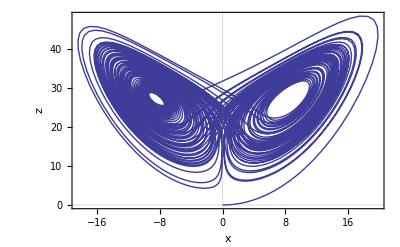

```mathematica
ListLinePlot[%3,PlotTheme->"Scientific",{PlotStyle->{ColorData[1][1],Thickness[Medium]}},FrameLabel->{"x","z"}]
```

```mathematica
Import["/Users/miguelangel/x(t).txt","Table"]
```

{{0.,0.},{0.01,0.0951214},{0.02,0.182772},{0.03,0.265977},6994,{69.98,-3.75364},{69.99,-3.96195},{70.,-4.1799}}
 |  |  |  |

```mathematica
Import["/Users/miguelangel/y(t).txt","Table"]
```

{{0.,1.},{0.01,1.00354},{0.02,1.03242},{0.03,1.08474},6994,{69.98,-5.79442},{69.99,-6.09038},{70.,-6.41328}}
 |  |  |  |

```mathematica
Import["/Users/miguelangel/z(t).txt","Table"]
```

{{0.,0.},{0.01,0.000479006},{0.02,0.00186843},{0.03,0.00416733},6994,{69.98,18.9265},{69.99,18.6546},{70.,18.4149}}
 |  |  |  |

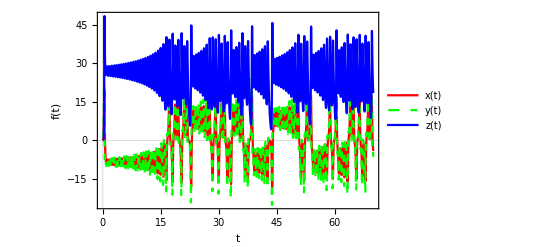

```mathematica
ListLinePlot[{%5,%6,%7},PlotTheme->"Scientific",PlotStyle->{Red,{Green,Dashed},Blue},FrameLabel->{"t","f(t)"},PlotLegends->{"x(t)","y(t)","z(t)"}]
```

```mathematica
Import["/Users/miguelangel/map.txt","Table"]
```

{{48.3081,28.7884},{28.7884,28.8933},{28.8933,29.0103},{29.0103,29.1361},{29.1361,29.2701},{29.2701,29.4131},{29.4131,29.5658},{29.5658,29.7288},{29.7288,29.908},{29.908,30.1012},{30.1012,30.3062},{30.3062,30.5313},{30.5313,30.7735},{30.7735,31.0439},{31.0439,31.3384},{31.3384,31.6626},{31.6626,32.0245},{32.0245,32.4306},{32.4306,32.9026},{32.9026,33.4443},{33.4443,34.1021},{34.1021,34.8871},{34.8871,35.9359},{35.9359,37.4232},{37.4232,40.1293},{40.1293,39.1814},{39.1814,41.4835},{41.4835,36.9299},{36.9299,39.098},{39.098,41.6805},{41.6805,36.6488},{36.6488,38.6048},{38.6048,44.702},{44.702,32.8557},{32.8557,33.3795},{33.3795,34.0278},{34.0278,34.7984},{34.7984,35.8003},{35.8003,37.2277},{37.2277,39.7165},{39.7165,40.0501},{40.0501,39.3325},{39.3325,41.0171},{41.0171,37.6314},{37.6314,40.6335},{40.6335,38.2325},{38.2325,42.789},{42.789,35.1586},{35.1586,36.2844},{36.2844,37.969},{37.969,41.6754},{41.6754,36.6663},{36.6663,38.6227},{38.6227,44.3796},{44.3796,33.1668},{33.1668,33.7629},{33.7629,34.4809},{34.4809,35.3939},{35.3939,36.5992},{36.5992,38.5143},{38.5143,45.6622},{45.6622,31.7313},{31.7313,32.0932},{32.0932,32.5138},{32.5138,32.9981},{32.9981,33.5556},{33.5556,34.2323},{34.2323,35.0706},{35.0706,36.1664},{36.1664,37.7826},{37.7826,41.0551},{41.0551,37.5856},{37.5856,40.5307}}

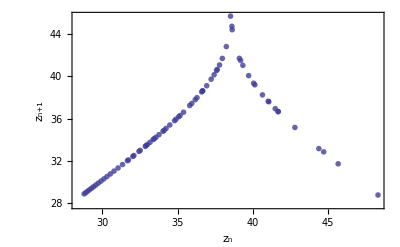

```mathematica
ListPlot[%9,PlotTheme->"Scientific",PlotStyle->{ColorData[1][1],Opacity[0.8],PointSize[0.01]},FrameLabel->{Subscript[z,n],Subscript[z,n+1]}]
```

```mathematica
Import["/Users/miguelangel/semilogdelta.txt","Table"]
```

{{0.,-27.631},{0.01,-27.6181},{0.02,-27.5817},{0.03,-27.5258},6994,{69.98,2.22178},{69.99,2.25486},{70.,2.2793}}
 |  |  |  |

```mathematica
Import["/Users/miguelangel/recta.txt","Table"]
```

{{0.,-40.2055},{0.01,-40.1962},{0.02,-40.1868},{0.03,-40.1775},6994,{69.98,25.2693},{69.99,25.2787},{70.,25.288}}
 |  |  |  |

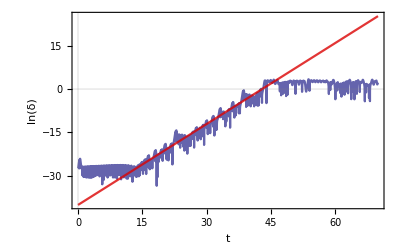

```mathematica
ListLinePlot[{%11,%12},PlotTheme->"Scientific",PlotStyle->{{ColorData[1][1],Opacity[0.8]},{ColorData[2][1],Opacity[0.8]}},FrameLabel->{t,"ln(δ)"}]
```

```mathematica
Import["/Users/miguelangel/atractor3Dd.txt","Table"]
```

{{1.×10^-12,1.,1.×10^-12},{0.0951214,1.00354,0.000479006},6997,{-13.4959,-18.3856,27.8129},{-13.9497,-18.1083,29.5558}}
 |  |  |  |

```mathematica
b=Graphics3D[{ColorData[2][1],Thickness[Medium],Line[%14]},Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
Import["/Users/miguelangel/atractor2Dd.txt","Table"]
```

{{1.×10^-12,1.×10^-12},{0.0951214,0.000479006},{0.182772,0.00186843},6995,{-12.9774,26.0916},{-13.4959,27.8129},{-13.9497,29.5558}}
 |  |  |  |

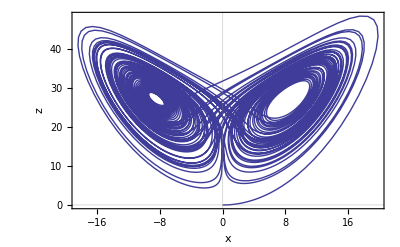

```mathematica
ListLinePlot[%16,PlotTheme->"Scientific",{PlotStyle->{ColorData[1][1],Thickness[Medium]}},FrameLabel->{"x","z"}]
```

```mathematica
Import["/Users/miguelangel/x(t)d.txt","Table"]
```

{{0.,1.×10^-12},{0.01,0.0951214},{0.02,0.182772},{0.03,0.265977},6994,{69.98,-12.9774},{69.99,-13.4959},{70.,-13.9497}}
 |  |  |  |

```mathematica
Import["/Users/miguelangel/y(t)d.txt","Table"]
```

{{0.,1.},{0.01,1.00354},{0.02,1.03242},{0.03,1.08474},6994,{69.98,-18.4314},{69.99,-18.3856},{70.,-18.1083}}
 |  |  |  |

```mathematica
Import["/Users/miguelangel/z(t)d.txt","Table"]
```

{{0.,1.×10^-12},{0.01,0.000479006},{0.02,0.00186843},{0.03,0.00416733},6994,{69.98,26.0916},{69.99,27.8129},{70.,29.5558}}
 |  |  |  |

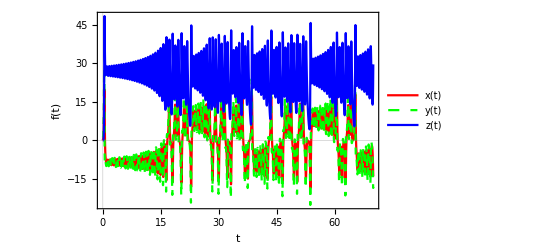

```mathematica
ListLinePlot[{%18,%19,%20},PlotTheme->"Scientific",PlotStyle->{Red,{Green,Dashed},Blue},FrameLabel->{"t","f(t)"},PlotLegends->{"x(t)","y(t)","z(t)"}]
```

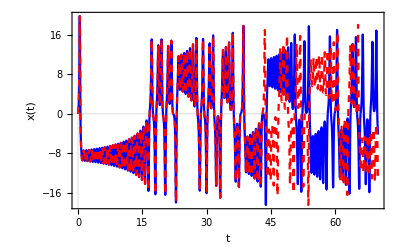

```mathematica
ListLinePlot[{%5,%18},PlotTheme->"Scientific",PlotStyle->{Blue,{Red,Dashed}},FrameLabel->{"t","x(t)"}]
```

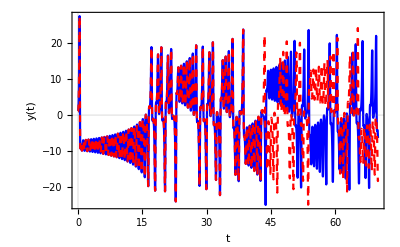

```mathematica
ListLinePlot[{%6,%19},PlotTheme->"Scientific",PlotStyle->{Blue,{Red,Dashed}},FrameLabel->{"t","y(t)"}]
```

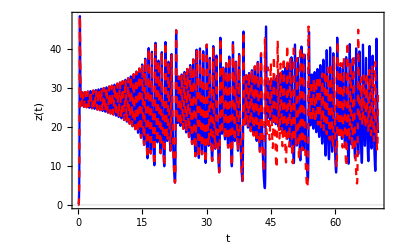

```mathematica
ListLinePlot[{%7,%20},PlotTheme->"Scientific",PlotStyle->{Blue,{Red,Dashed}},FrameLabel->{"t","z(t)"}]
```

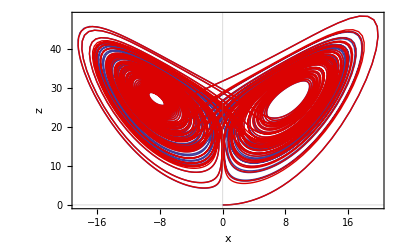

```mathematica
ListLinePlot[{%3,%16},PlotTheme->"Scientific",{PlotStyle->{{ColorData[1][1],Thickness[Medium]},{ColorData[2][1],Thickness[Medium]}}},FrameLabel->{"x","z"}]
```

```mathematica
Show[a,b]
```

-Graphics3D-

## ρ<1, σ=10, β=8/3

### ρ=0.9, x(0)=-10, y(0)=10, z(0)=5

```mathematica
Import["/Users/miguelangel/1atractor3D.txt","Table"]
```

{{-10.,10.,5.},{-8.08469,10.2224,3.96714},{-6.33742,10.3105,3.13349},4996,{-0.00147375,-0.00146024,8.66598×10^-7},{-0.0014724,-0.00145891,8.65011×10^-7}}
 |  |  |  |

```mathematica
c=Graphics3D[{ColorData[1][1],Thickness[Medium],Line[%27]},Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

### ρ=0.9, x(0)=10, y(0)=3, z(0)=-4

```mathematica
Import["/Users/miguelangel/2atractor3D.txt","Table"]
```

{{10.,3.,-4.},{9.35487,3.42196,-3.58798},{8.80784,3.77444,-3.17103},4996,{0.00271455,0.00268967,2.94012×10^-6},{0.00271207,0.0026872,2.93473×10^-6}}
 |  |  |  |

```mathematica
d=Graphics3D[{ColorData[2][1],Thickness[Medium],Line[%29]},Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
Show[c,d]
```

-Graphics3D-

```mathematica
Import["/Users/miguelangel/1x(t).txt","Table"]
```

{{0.,-10.},{0.01,-8.08469},{0.02,-6.33742},{0.03,-4.75252},4994,{49.98,-0.00147511},{49.99,-0.00147375},{50.,-0.0014724}}
 |  |  |  |

```mathematica
Import["/Users/miguelangel/2x(t).txt","Table"]
```

{{0.,10.},{0.01,9.35487},{0.02,8.80784},{0.03,8.34342},4994,{49.98,0.00271704},{49.99,0.00271455},{50.,0.00271207}}
 |  |  |  |

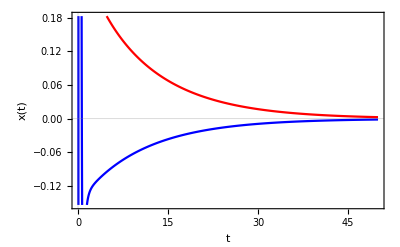

```mathematica
ListLinePlot[{%32,%33},PlotTheme->"Scientific",PlotStyle->{Blue,Red},FrameLabel->{"t","x(t)"}]
```

## 1<ρ<ρH, σ=10, β=8/3

### ρ=14, x(0)=0, y(0)=1, z(0)=0

```mathematica
Import["/Users/miguelangel/3atractor3D.txt","Table"]
```

{{0.,1.,0.},{0.0949009,0.996785,0.000476834},{0.181086,1.00619,0.00183556},4996,{-5.88784,-5.88784,13.},{-5.88784,-5.88784,13.}}
 |  |  |  |

```mathematica
Graphics3D[{ColorData[1][1],Thickness[Medium],Line[%35]},Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
Import["/Users/miguelangel/3x(t).txt","Table"]
```

{{0.,0.},{0.01,0.0949009},{0.02,0.181086},{0.03,0.260525},4994,{49.98,-5.88784},{49.99,-5.88784},{50.,-5.88784}}
 |  |  |  |

```mathematica
Import["/Users/miguelangel/3y(t).txt","Table"]
```

{{0.,1.},{0.01,0.996785},{0.02,1.00619},{0.03,1.02701},4994,{49.98,-5.88784},{49.99,-5.88784},{50.,-5.88784}}
 |  |  |  |

```mathematica
Import["/Users/miguelangel/3z(t).txt","Table"]
```

{{0.,0.},{0.01,0.000476834},{0.02,0.00183556},{0.03,0.00400845},4994,{49.98,13.},{49.99,13.},{50.,13.}}
 |  |  |  |

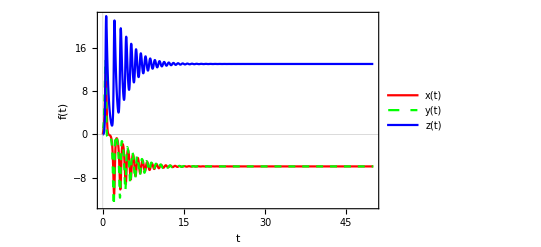

```mathematica
ListLinePlot[{%37,%38,%39},PlotTheme->"Scientific",PlotStyle->{Red,{Green,Dashed},Blue},FrameLabel->{"t","f(t)"},PlotLegends->{"x(t)","y(t)","z(t)"}]
```

## Bifurcation Diagrams

```mathematica
Import["/Users/miguelangel/bifurcacionesx.txt","Table"]
```

{{0.,0.770968},{1.,1.16809×10^-106},{1.,1.16809×10^-106},{1.,1.16809×10^-106},{1.,1.16809×10^-106},3428364,{250.,-48.2638},{250.,38.7134},{250.,-48.2641},{250.,38.7135},{250.,-48.2641}}
 |  |  |  |

```mathematica
Import["/Users/miguelangel/bifurcacionesy.txt","Table"]
```

{{1.,1.16809×10^-106},{1.,1.16809×10^-106},{1.,1.16809×10^-106},{1.,1.16809×10^-106},{1.,1.16809×10^-106},3838982,{250.,-25.1837},{250.,-15.0415},{250.,-97.8715},{250.,55.8763},{250.,51.8386}}
 |  |  |  |

```mathematica
Import["/Users/miguelangel/bifurcacionesz.txt","Table"]
```

{{0.,0.135588},{1.,5.11662×10^-213},{1.,5.11662×10^-213},{1.,5.11662×10^-213},{1.,5.11662×10^-213},3630853,{250.,328.398},{250.,215.064},{250.,299.464},{250.,175.247},{250.,328.398}}
 |  |  |  |

```mathematica
ListPlot[%41,PlotRange->All,PlotTheme->"Scientific",PlotStyle->{Gray,Opacity[0.1],PointSize[0.001]},FrameLabel->{"ρ","x"}]
```

-Graphics-

```mathematica
ListPlot[%42,PlotRange->All,PlotTheme->"Scientific",PlotStyle->{Gray,Opacity[0.1],PointSize[0.001]},FrameLabel->{"ρ","y"}]
```

-Graphics-

```mathematica
ListPlot[%43,PlotRange->All,PlotTheme->"Scientific",PlotStyle->{Gray,Opacity[0.1],PointSize[0.001]},FrameLabel->{"ρ","z"}]
```

-Graphics-

## Simulation:

```mathematica
Manipulate[Clear[x,y,z,t];
Module[{soln},
With[{b=bb,σ=σσ,r=rr,x0=xx0,y0=yy0,z0=zz0},soln=Quiet@NDSolve[SetPrecision[{x'[t]==σ (-x[t]+y[t]),y'[t]==r x[t]-y[t]-x[t] z[t],z'[t]==x[t] y[t]-b z[t],x[0]==x0,y[0]==y0,z[0]==z0},Infinity],{x[t],y[t],z[t]},{t,0,tt},PrecisionGoal->ControlActive[4,8],WorkingPrecision->ControlActive[MachinePrecision,20]];ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.soln],{t,0,soln[[1,1,2,0,1,1,2]]},PlotPoints->ControlActive[100,200],MaxRecursion->ControlActive[4,6],Axes->False,Boxed->False,ImageSize->{400,400},PlotRange->All]]],{{tt,10,"time"},1,35,.01,ImageSize->Small,Appearance->"Labeled"},
Delimiter,
Style["parameters",Bold],
{{bb,8/3,"b"},0,10,.01,ImageSize->Small,Appearance->"Labeled"},{{σσ,10,"σ"},0,100,.01,ImageSize->Small,Appearance->"Labeled"},{{rr,28,"r"},0,100,.01,ImageSize->Small,Appearance->"Labeled"},Delimiter,Style["initial conditions",Bold],
{{xx0,1,"x_0"},1,200,.01,ImageSize->Small,Appearance->"Labeled"},{{yy0,5,"y_0"},1,200,.01,ImageSize->Small,Appearance->"Labeled"},{{zz0,10,"z_0"},1,200,.01,ImageSize->Small,Appearance->"Labeled"},ControlPlacement->Left,AutorunSequencing->{3,4,5},TrackedSymbols->Manipulate]
```